## Release Notes

challenge1-3 : Try the full case - wow, did this fail!
challenge1-2 : Add in a constant term to the fits. 
challenge1-1 : Periodogram to find periods (PMC.m extended to eliminate dead Gaussians)

## Setup

```mathematica
(* Initialize stuff *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["PMC`"];
Needs["GLSTools`"];
```

## Data

```mathematica
(* Read in data *)
vrad =SemanticImport["vrad_simu_challenge_inclination_90_1.rdb",ExcludedLines->{2}];
```

```mathematica
Keys[vrad][[1]]//Normal
```

{jdb,rv,sig_rv,fwhm,sig_fwhm,bis_span,sig_bis_span,rhk,sig_rhk,rv_osc_and_gran,rv_activity,rv_planet,rv_inst_noise,fwhm_osc_and_gran,fwhm_activity,fwhm_inst_noise,bis_span_osc_and_gran,bis_span_activity,bis_span_inst_noise,rhk_osc_and_gran,rhk_activity,rhk_inst_noise}

```mathematica
(* Extract columns we want *)
```

```mathematica
data = Normal@vrad[All,#]&/@ {"jdb",1000(#"rv")&,1/(1000 #"sig_rv")^2&};
```

```mathematica
Clear[plot1];
plot1[logP_]:=ListPlot[Transpose[{FractionalPart[data[[1]]/Exp[logP]],data[[2]]}]]
```

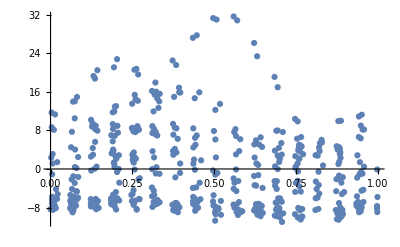

```mathematica
plot1[Log[16]]
```

```mathematica
(* Work out fundamental frequency, standard deviation, max time *)
tmax = Max@data[[1]] - Min@data[[1]];
ffreq = 2 Pi/Max@data[[1]];
sddata = StandardDeviation[data[[2]]];
sdslope = sddata/tmax;
mdata = Mean@data[[2]];
```

```mathematica
data[[3]] = ConstantArray[1/sddata^2,Length@data[[3]]];
```

## Simple periodogram

```mathematica
freqs = Range[ffreq,0.5,ffreq]; (* Arbitrary cutoff at half a day *)
pgram=GLS[data[[1]],data[[2]], data[[3]], freqs];
pfap = FAP[data[[1]],data[[2]], data[[3]],freqs,50];
```

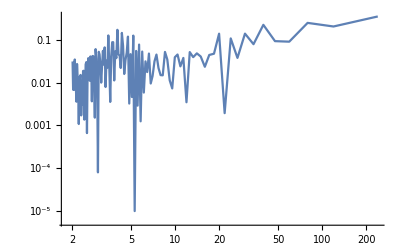

```mathematica
ListLogLogPlot[Transpose[{1/freqs,pgram}],Joined->True,PlotRange->Full]
```

```mathematica
Quantile[pfap,0.95]
```

0.0115685

```mathematica
1/freqs[[10;;20]]
```

{23.8747,21.7042,19.8956,18.3651,17.0533,15.9164,14.9217,14.0439,13.2637,12.5656,11.9373}

```mathematica
pgram[[10;;20]]
```

{0.108639,0.0019283,0.140184,0.0476511,0.0444849,0.0235459,0.0409495,0.0485134,0.0395321,0.0519754,0.00347313}

```mathematica
trials = Select[Transpose[{freqs,pgram}],#[[2]]>Quantile[pfap,0.95]&];
Length@trials
```

85

## Model

```mathematica
Clear[rvmodel,chi2];
rvmodel[phi_,lfreq_,logK_,c0_]:=Module[{f,K=Exp[logK]},
f = 2 Pi (FractionalPart[data[[1]]Exp[lfreq]]+phi);
K Cos[f]+c0
]
chi2[phi_?NumericQ,lfreq_?NumericQ,logK_?NumericQ,c0_?NumericQ]:=Module[{rv},
rv = rvmodel[phi,lfreq,logK,c0];
Total[(data[[2]]- rv)^2*data[[3]]]
]
```

## Refinement

```mathematica
mins=NMinimize[{chi2[p,l,k,c0],p≥0,p<1,l>Log[ffreq]},{{p,0,1},{l,Log[0.8 #],Log[1.2 #]},{k,-5,5},{c0,mdata-sddata,mdata+sddata}},PrecisionGoal->2,AccuracyGoal->1]&/@trials[[1;;20,2]]
```

{{410.053,{p→0.386506,l→-3.40611,k→1.56439,c0→-0.0428726}},{443.468,{p→0.426774,l→-3.63263,k→1.27684,c0→-0.136674}},{374.133,{p→0.309442,l→-5.27177,k→1.81808,c0→-1.32919}},{417.775,{p→0.19997,l→-3.30712,k→1.51344,c0→0.0262582}},{376.586,{p→0.401644,l→-4.8548,k→1.75388,c0→0.109139}},{438.454,{p→0.486454,l→-3.53631,k→1.36345,c0→-0.233673}},{417.775,{p→0.19997,l→-3.30712,k→1.51344,c0→0.0262596}},{476.968,{p→0.0276903,l→-2.376,k→0.71726,c0→0.0565539}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381683}},{475.744,{p→0.393275,l→-2.17761,k→0.779923,c0→-0.142655}},{468.142,{p→0.,l→-2.77818,k→0.405916,c0→-0.166221}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381682}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381683}},{417.775,{p→0.19997,l→-3.30712,k→1.51344,c0→0.0262617}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381683}},{413.122,{p→0.317914,l→-3.48982,k→1.54049,c0→0.16479}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381683}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381681}},{402.094,{p→0.269874,l→-3.23734,k→1.61677,c0→0.381683}},{374.152,{p→0.308223,l→-5.27156,k→1.83136,c0→-1.35822}}}

## PMC

### Initialize

```mathematica
npop=10000;
mix = {1,{p,l,k,c0}/.#,DiagonalMatrix[{0.1,0.1,0.3,sddata/2}]} &/@ mins[[All,2]];
model= buildModels@mix;
eps = DiagonalMatrix[{0.01,0.001,0.01,0.001}^2];
Clear[fiddle];
fiddle[x_,y_,z_,c0_] := {Mod[x,1],y,z,c0};
fiddle[-0.9,10,10,0]
```

{0.1,10,10,0}

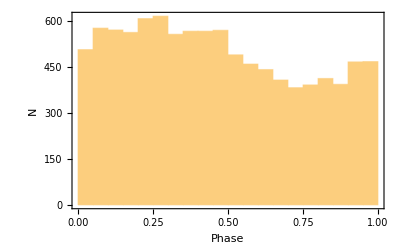

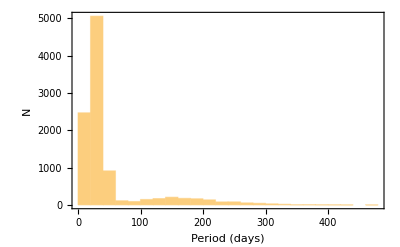

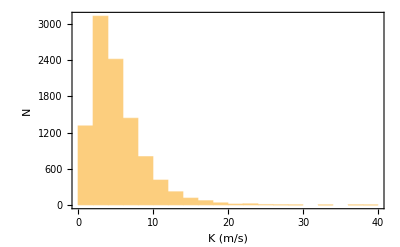

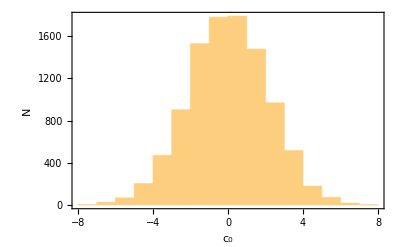

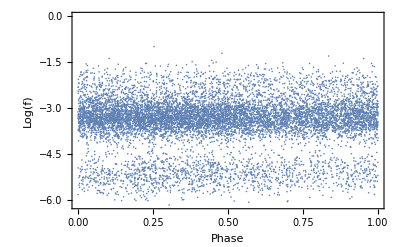

```mathematica
xx = mkRandom[model,npop, fiddle]; (* One off for simplicity *)
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[Exp[-xx[[All,2]]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
Histogram[xx[[All,4]],Frame->True,Axes->False,FrameLabel->{"c_0","N"}]
(*Histogram[xx[[All,5]],Frame->True,Axes->False,FrameLabel->{"c_1","N"}]*)
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Log(f)"}]
```

### Loop

```mathematica
{perplex,xx,model}=iterPMC[chi2,npop,model,eps,fiddle,100];
```

Iteration:0 0.000122918 {0.556099,-5.61162,1.68284,3.08682}

Number of components:6

Iteration:1 0.00452749 {0.4528,-5.59566,1.73903,1.39723}

Number of components:6

Iteration:2 0.000126601 {0.487283,-5.6027,1.84322,1.37891}

Number of components:3

Iteration:3 0.0780903 {0.492587,-5.6034,1.85111,1.37172}

Number of components:2

Iteration:4 0.0163663 {0.495,-5.60394,1.88938,1.35649}

Number of components:2

Iteration:5 0.00593089 {0.527053,-5.61139,1.90833,1.21277}

Number of components:2

Iteration:6 0.00798332 {0.527243,-5.61325,1.97747,1.00811}

Number of components:2

Iteration:7 0.0601728 {0.549193,-5.61948,2.03143,0.840726}

Number of components:2

Iteration:8 0.639058 {0.552117,-5.62075,2.03513,1.01543}

Number of components:2

Iteration:9 0.963709 {0.551653,-5.62061,2.0371,1.03474}

Number of components:2

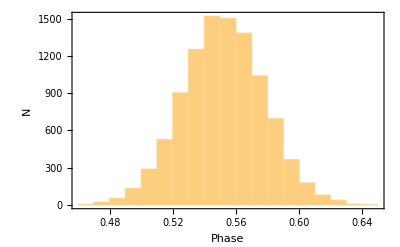

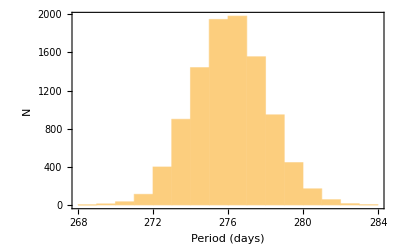

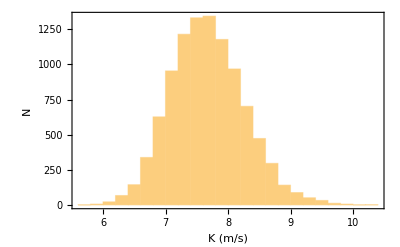

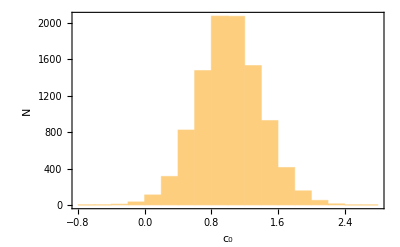

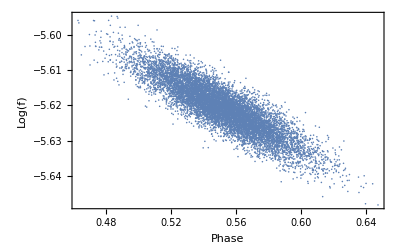

```mathematica
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[Exp[-xx[[All,2]]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
Histogram[xx[[All,4]],Frame->True,Axes->False,FrameLabel->{"c_0","N"}]
(*Histogram[xx[[All,5]],Frame->True,Axes->False,FrameLabel->{"c_1","N"}]*)
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Log(f)"}]
```